## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

## General purpose functions

```mathematica
XYtoList[x_,y_]:=If[Length[x]==Length[y],Table[{x[[i]],y[[i]]},{i,1,Length[x]}]]
listtoXYlist[x_]:=Table[{{x[[i,1]]},x[[i,2]]},{i,1,Length[x]}]
```

```mathematica
Z[s_]:=ElementData[s,"AtomicNumber"]
e[z_]:="Element " <> ToString[ElementData[z,"Abbreviation"]]
e2[z_]:= ToString[ElementData[z,"Abbreviation"]]
A[s_]:=ElementData[s,"AtomicWeight"]
```

## Load NIST database

Import the f1 & f2 NIST database file (combination of Chantler 1995 and 2000 tables)

```mathematica
NISTdb=Import["f1f2_NIST.dat","Table"];
```

Deal with formatting of database file

```mathematica
NISTdbseps=DeleteCases[Table[If[StringTake[ToString[NISTdb[[x,1]]],2]=="//",x,0],{x,1,Length[NISTdb]}],0];
```

Function to extract desired column of data

```mathematica
NIST[z_]:=NISTdb[[NISTdbseps[[3*z]]+1;;If[z<92,NISTdbseps[[3*z+1]]-1,-1]]]
```

Make tables of f1, f2 and mu values

```mathematica
NISTf1=Table[XYtoList[NIST[i][[All,1]]*1000,NIST[i][[All,2]]],{i,1,91,1}];
NISTf2=Table[XYtoList[NIST[i][[All,1]]*1000,-NIST[i][[All,3]]],{i,1,91,1}];
NISTmu=Table[XYtoList[NIST[i][[All,1]]*1000,NIST[i][[All,4]]],{i,1,91,1}];
```

```mathematica
Manipulate[ListLogLinearPlot[{NISTf1[[i]],NISTf2[[i]]},PlotRange->{All,{-60,100}},PlotLabel->e2[i]<>", f1, f2"],{i,1,91,1}]
```

## Padded interpolation function for f2

Provided a data table of the form (Energy, f2), this function automatically pads the low and high energy behaviours

```mathematica
PaddedInterpFunction[data_,x_]:=Piecewise[{{data[[1,2]],x<data[[1,1]]},{data[[-1,2]]*(x/data[[-1,1]])^-2,x>data[[-1,1]]}}, Interpolation[data,InterpolationOrder->1][x]]
```

Define some functions to get data

```mathematica
Energies[Z_]:=NISTf2[[Z]][[All,1]]; (*Gives an array of containing the NIST tabulation energies for a given element *)
fIm[Z_,x_]:=PaddedInterpFunction[NISTf2[[Z]],x]; (*Gives a padded function so that fIm can be evaluated for any energy and any element *)
```

We can see how the padding affects the tabulated data.

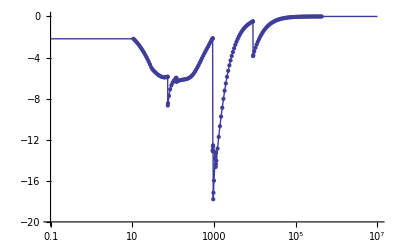

```mathematica
Show[{LogLinearPlot[fIm[29,x],{x,.1,10000000},PlotRange->{All,{-20,0}}],ListLogLinearPlot[NISTf2[[29]]]}]
```

For example, this makes it simple to plot f2 for numerous elements

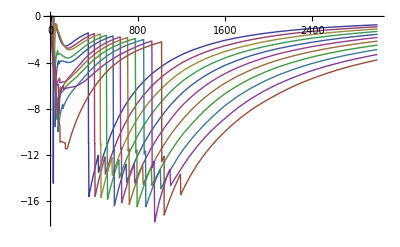

```mathematica
Plot[Evaluate[Table[fIm[z,x],{z,20,30}]],{x,0,3000}]
```

## Define Kramers - Kronig Transform Function

This function takes two inputs: the atomic number Z and a list of energies at which to evaluate the Kramers-Kronig integral
It returns two ouputs: the first is a table with the format (E, fRe(E)) and the second is the linear interpolation function for this data (so evaluations can be done at any E within the range)

The numerical integration strategy was chosen so that results are in fair agreement with the tabulated fRe over a wide range of energies. It may be necessary to modify the strategy if focusing the calculation in a particular energy range. 
The calculation is set up to evaluate the integral on as many processor cores as available and will dynamically display a progress bar. 

If many errors are being output during the evaluation (usually integral convergance) then the integration strategy is probably at fault. Typically when this happens the output is still valid for many of the requested energies and a few outliers are present.   

Due to some randomness in the BisectionDithering method of AdaptvieMonteCarlo, the results can vary slightly.7fon different calculation runs. For precisely reproducible results, a different integration strategy may be preferable. This is simply a “general purpose” approach that seems to eliminate errors for calculations of many different elements.

```mathematica
KramersKronigNIST[Z_,OutputEnergy_]:=
(
fImInternal[t_]=fIm[Z,t];
fReCALC[x_]:=Z+2.0/π*NIntegrate[t*fImInternal[t]/(t^2-x^2),{t,0,x, Infinity},Method->{"PrincipalValue",Method->{"AdaptiveMonteCarlo","BisectionDithering"->1/8}},MaxRecursion->150];
Clear[counter];SetSharedVariable[counter];counter=1;
fReTXAS=N[Monitor[ParallelTable[counter++;{x,Quiet[fReCALC[x]]},{x,OutputEnergy},Method->"CoarsestGrained"],ProgressIndicator[counter,{1,Length[OutputEnergy]}] ]];
fReXASinterp=Interpolation[fReTXAS,InterpolationOrder->1];
{fReTXAS,fReXASinterp}
);
```

## Test the numerical Kramers-Kronig method for a few elements

Oxygen

```mathematica
{fReCalcO,fReCalcOInterp}=KramersKronigNIST[8,Energies[8]];
```

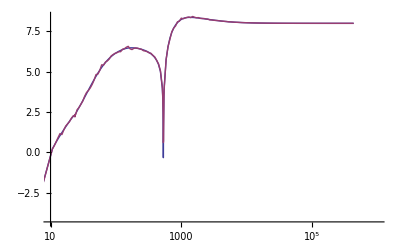

```mathematica
ListLogLinearPlot[{NISTf1[[8]],fReCalcO},PlotRange->{{10,10^6},All},Joined->True]
```

Copper

```mathematica
{fReCalcCu,fReCalcCuInterp}=KramersKronigNIST[29,Energies[29] ];
```

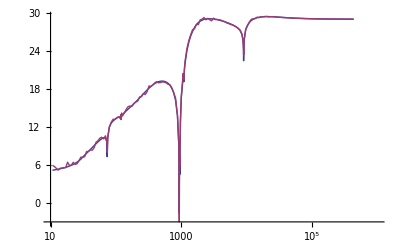

```mathematica
ListLogLinearPlot[{NISTf1[[29]],fReCalcCu},PlotRange->{{10,10^6},All},Joined->True]
```

Barium

```mathematica
{fReCalcBa,fReCalcBaInterp}=KramersKronigNIST[56,Energies[56] ];
```

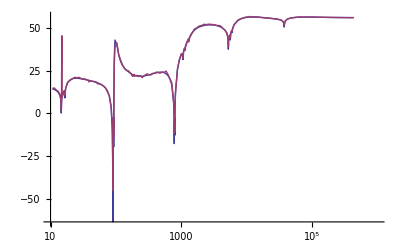

```mathematica
ListLogLinearPlot[{NISTf1[[56]],fReCalcBa},PlotRange->{{10,10^6},All},Joined->True]
```

Carbon

```mathematica
{fReCalcC,fReCalcCInterp}=KramersKronigNIST[6,Energies[6] ]//Quiet;
```

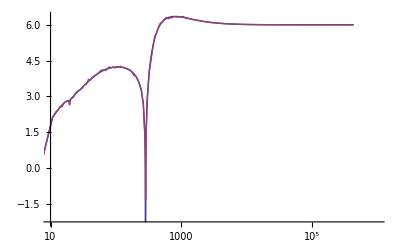

```mathematica
ListLogLinearPlot[{NISTf1[[6]],fReCalcC},PlotRange->{{10,10^6},All},Joined->True]
```

Potassium

```mathematica
{fReCalcK,fReCalcKInterp}=KramersKronigNIST[19,Energies[19] ]//Quiet;
```

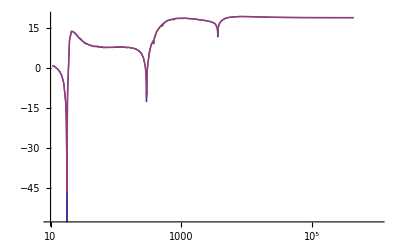

```mathematica
ListLogLinearPlot[{NISTf1[[19]],fReCalcK},PlotRange->{{10,10^6},All},Joined->True]
```

Lead

```mathematica
{fReCalcPb,fReCalcPbInterp}=KramersKronigNIST[82,Energies[82] ]//Quiet;
```

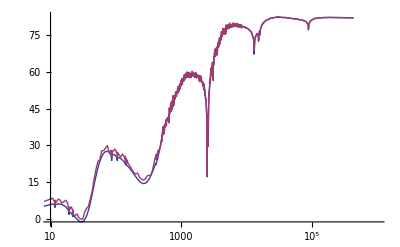

```mathematica
ListLogLinearPlot[{NISTf1[[82]],fReCalcPb},PlotRange->{{10,10^6},All},Joined->True]
```